```mathematica
t=Import["D:\\data.txt","Table"];
```

```mathematica
Length[t]
```

500001

```mathematica
t=Table[t[[i]],{i,1,Length[t],10}];
t=Take[t,20000]
```

{{1.41421,0.},{1.41421,0.01},{1.41421,0.02},{1.41421,0.03},{1.41421,0.04},19991,{1.6243,-0.19643},{1.63428,-0.197075},{1.64426,-0.19772},{1.65424,-0.198365}}
 |  |  |  |

```mathematica
Length[t]
```

20000

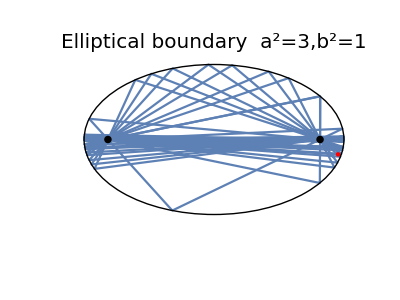

```mathematica
g1=ListPlot[t,PlotRange->All,AxesLabel->{"x","y"},Axes->False]/.Point->Line;
g2=Graphics[{Red,Disk[t[[-1]],0.03]}];
g4=Graphics[{Thick,Black,Circle[{0,0},{√3,1}],Black,Disk[{-√2,0},0.05],Black,Disk[{√2,0},0.05]}];
g3=Graphics[Text[Style["Elliptical boundary  "<>"a^2=3,b^2=1",20],{0,1.3}]];
Show[g1,g2,g3,g4,PlotRange->{{-2,2},{-1.5,1.5}},AspectRatio->Automatic]
```

```mathematica
pict={};
Do[
temp=Take[t,i];
g1=ListPlot[temp,PlotRange->All,AxesLabel->{"x","y"},Axes->False]/.Point->Line;
g2=Graphics[{Red,Disk[temp[[-1]],0.05]}];
g4=Graphics[{Thick,Black,Circle[{0,0},{√3,1}],Black,Disk[{-√2,0},0.05],Black,Disk[{√2,0},0.05]}];
g3=Graphics[Text[Style["Elliptical boundary "<>"a^2=3,b^2=1",20],{0,1.3}]];
g=Show[g1,g2,g3,g4,PlotRange->{{-2,2},{-1.5,1.5}},AspectRatio->Automatic];
AppendTo[pict,g];
Print[i,"/",Length[t]],

{i,1,Length[t],Floor[Length[t]/100]}];
Export["C:\\Users\\ChenYangyao\\Desktop\\pic_ch3_lorenz\\mma3d\\a2.gif",pict]
```

1/20000

201/20000

401/20000

601/20000

801/20000

1001/20000

1201/20000

1401/20000

1601/20000

1801/20000

2001/20000

2201/20000

2401/20000

2601/20000

2801/20000

3001/20000

3201/20000

3401/20000

3601/20000

3801/20000

4001/20000

4201/20000

4401/20000

4601/20000

4801/20000

5001/20000

5201/20000

5401/20000

5601/20000

5801/20000

6001/20000

6201/20000

6401/20000

6601/20000

6801/20000

7001/20000

7201/20000

7401/20000

7601/20000

7801/20000

8001/20000

8201/20000

8401/20000

8601/20000

8801/20000

9001/20000

9201/20000

9401/20000

9601/20000

9801/20000

10001/20000

10201/20000

10401/20000

10601/20000

10801/20000

11001/20000

11201/20000

11401/20000

11601/20000

11801/20000

12001/20000

12201/20000

12401/20000

12601/20000

12801/20000

13001/20000

13201/20000

13401/20000

13601/20000

13801/20000

14001/20000

14201/20000

14401/20000

14601/20000

14801/20000

15001/20000

15201/20000

15401/20000

15601/20000

15801/20000

16001/20000

16201/20000

16401/20000

16601/20000

16801/20000

17001/20000

17201/20000

17401/20000

17601/20000

17801/20000

18001/20000

18201/20000

18401/20000

18601/20000

18801/20000

19001/20000

19201/20000

19401/20000

19601/20000

19801/20000

C:\Users\ChenYangyao\Desktop\pic_ch3_lorenz\mma3d\a2.gif